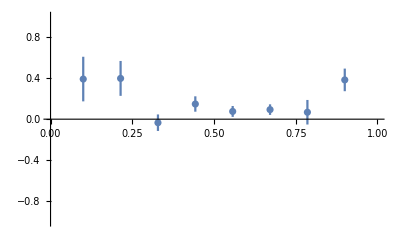

```mathematica
Needs["ErrorBarPlots`"];
data = Import["/home/jhell/research/results/steadyStateFlow/ballRuns/attempt1/0/overallData.dat", "Data"];
ErrorListPlot[data, PlotRange->{{0,1}, {-1,1}}]
```

```mathematica
Manipulate[Plot[1+ζ ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{0,1}], {ζ, 0, 1}]
```

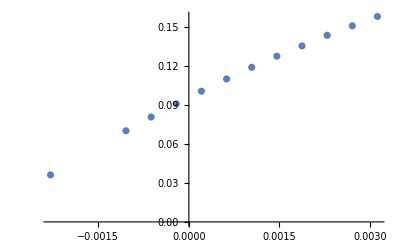

```mathematica
Needs["ErrorBarPlots`"];
newData = Import["/home/jhell/research/results/steadyStateFlow/newTests/attempt9/0/0/mathFormatData.dat", "Data"];
ErrorListPlot[newData]
```